Universal Quantum Computation: Demonstration |

Here we provide a simple demonstration that any arbitrary unitary operation can be implemented by combining CNOT gate and single-qubit rotations.

GivensFactorpaclet:Q3/ref/GivensFactorQ3 Package Symbol | Decomposes a unitary operator into a list of Givens rotations
GivensRotationpaclet:Q3/ref/GivenRotationQ3 Package Symbol | Represents a Givens rotation, that is, a two-level unitary operator

Some functions conveniently used for the demonstration of universal quantum computation.

### Step 1. Decomposition into two-Level unitary operations

We first decompose the unitary operation into two-level unitary operations, that is, unitary operators acting only on a two-dimensional subspace.

```mathematica
<<Q3`
```

```mathematica
Let[Qubit,S]
```

Let us consider a system of n qubits.

```mathematica
$n=2;
$N=Power[2,$n];
kk=Range[$n];
SS=S[kk,$]
```

{S_(,,1),S_(,,2)}

Consider a 2^n×2^n unitary matrix.

```mathematica
mat=RandomUnitary[$N];
mat//MatrixForm
```

(0.0448453-0.670233 ⅈ | -0.296585+0.191826 ⅈ | -0.489917+0.416834 ⅈ | 0.0810764+0.0606181 ⅈ
-0.0403102+0.169813 ⅈ | 0.273647-0.704458 ⅈ | -0.296126+0.490761 ⅈ | -0.0217215-0.263412 ⅈ
0.397401+0.41397 ⅈ | -0.0802528+0.491481 ⅈ | -0.0938251+0.286795 ⅈ | 0.124835-0.5622 ⅈ
-0.133365-0.4138 ⅈ | -0.115647-0.206708 ⅈ | 0.188668-0.361999 ⅈ | 0.259763-0.72164 ⅈ)

This is an explicit operator expression of the unitary transformation.

```mathematica
opU=ExpressionFor[mat,SS]//Elaborate
```

(0.121108-0.452384 ⅈ)-(0.107167-0.157265 ⅈ) S_(,,1)^(,,X)S_(,,2)^(,,X)-(0.118785-0.107579 ⅈ) S_(,,1)^(,,X)S_(,,2)^(,,Y)+(0.0112132+0.325231 ⅈ) S_(,,1)^(,,X)S_(,,2)^(,,Z)-(0.118425+0.000358001 ⅈ) S_(,,1)^(,,Y)S_(,,2)^(,,X)-(0.0810226-0.333856 ⅈ) S_(,,1)^(,,Y)S_(,,2)^(,,Y)-(0.0148919+0.245311 ⅈ) S_(,,1)^(,,Y)S_(,,2)^(,,Z)-(0.1626-0.321459 ⅈ) S_(,,1)^(,,Z)S_(,,2)^(,,X)-(0.0555536+0.0481105 ⅈ) S_(,,1)^(,,Z)S_(,,2)^(,,Y)+(0.0311966-0.243553 ⅈ) S_(,,1)^(,,Z)S_(,,2)^(,,Z)-(0.0574712-0.0901709 ⅈ) S_(,,1)^(,,X)+(0.01346-0.198348 ⅈ) S_(,,1)^(,,Y)+(0.0381386-0.234961 ⅈ) S_(,,1)^(,,Z)-(0.00584789+0.14064 ⅈ) S_(,,2)^(,,X)+(0.0445469-0.0800267 ⅈ) S_(,,2)^(,,Y)-(0.145598-0.260665 ⅈ) S_(,,2)^(,,Z)

Here is a two-level decomposition, where the results are in terms of Givens rotations.

```mathematica
gg=GivensFactor[opU]
```

{0.863054-0.505112 ⅈ,GivensRotation[…],GivensRotation[…],GivensRotation[…],GivensRotation[…],GivensRotation[…],GivensRotation[…]}

You can convert the above results to more human readable full matrix form by means of Matrixpaclet:Q3/ref/MatrixQ3 Package Symbol.

```mathematica
mm=Matrix[gg,SS]//Chop;
MatrixForm/@mm
```

{(0.863054-0.505112 ⅈ | 0 | 0 | 0
0 | 0.863054-0.505112 ⅈ | 0 | 0
0 | 0 | 0.863054-0.505112 ⅈ | 0
0 | 0 | 0 | 0.863054-0.505112 ⅈ),(1. | 0 | 0 | 0
0 | 1. | 0 | 0
0 | 0 | 0.185956+0.775078 ⅈ | -0.130447-0.589626 ⅈ
0 | 0 | 0.130447-0.589626 ⅈ | 0.185956-0.775078 ⅈ),(1. | 0 | 0 | 0
0 | 0.16275-0.170353 ⅈ | 0.97185 | 0
0 | -0.97185 | 0.16275+0.170353 ⅈ | 0
0 | 0 | 0 | 1.),(1. | 0 | 0 | 0
0 | 1. | 0 | 0
0 | 0 | -0.780675+0.539182 ⅈ | -0.000429952+0.315959 ⅈ
0 | 0 | 0.000429952+0.315959 ⅈ | -0.780675-0.539182 ⅈ),(0.377247-0.555795 ⅈ | 0.740795 | 0 | 0
-0.740795 | 0.377247+0.555795 ⅈ | 0 | 0
0 | 0 | 1. | 0
0 | 0 | 0 | 1.),(1. | 0 | 0 | 0
0 | -0.476329+0.0212576 ⅈ | 0.87901 | 0
0 | -0.87901 | -0.476329-0.0212576 ⅈ | 0
0 | 0 | 0 | 1.),(1. | 0 | 0 | 0
0 | 1. | 0 | 0
0 | 0 | -0.972675+0.17244 ⅈ | 0.0604367+0.143234 ⅈ
0 | 0 | -0.0604367+0.143234 ⅈ | -0.972675-0.17244 ⅈ)}

Check the decomposition with the original matrix.

```mathematica
new=Dot@@mm;
mat-new//Chop//MatrixForm
```

(0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0)

### Step 2. Rewriting two-level unitary operators to elementary gates.

Now, we rewrite each two-level unitary operator in terms of elementary gates, that is, in a combination of CNOT gates and one controlled-U gate.

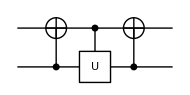
{0.863054-0.505112 ⅈ,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
gates=Expand/@gg
```

Here is a quantum circuit model of the decomposition. Here controlled-U gates are all labeled by the same character "U" but in fact they are different operators. Also do not forget to reverse the order of the elementary gates in the quantum circuit model.

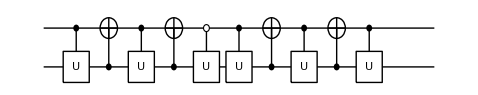

```mathematica
qc=QuantumCircuit[Sequence@@Reverse@gates]
```

```mathematica
new=ExpressionFor[qc]
```

(0.121108-0.452384 ⅈ)-(0.107167-0.157265 ⅈ) S_(,,1)^(,,X)S_(,,2)^(,,X)-(0.118785-0.107579 ⅈ) S_(,,1)^(,,X)S_(,,2)^(,,Y)+(0.0112132+0.325231 ⅈ) S_(,,1)^(,,X)S_(,,2)^(,,Z)-(0.118425+0.000358001 ⅈ) S_(,,1)^(,,Y)S_(,,2)^(,,X)-(0.0810226-0.333856 ⅈ) S_(,,1)^(,,Y)S_(,,2)^(,,Y)-(0.0148919+0.245311 ⅈ) S_(,,1)^(,,Y)S_(,,2)^(,,Z)-(0.1626-0.321459 ⅈ) S_(,,1)^(,,Z)S_(,,2)^(,,X)-(0.0555536+0.0481105 ⅈ) S_(,,1)^(,,Z)S_(,,2)^(,,Y)+(0.0311966-0.243553 ⅈ) S_(,,1)^(,,Z)S_(,,2)^(,,Z)-(0.0574712-0.0901709 ⅈ) S_(,,1)^(,,X)+(0.01346-0.198348 ⅈ) S_(,,1)^(,,Y)+(0.0381386-0.234961 ⅈ) S_(,,1)^(,,Z)-(0.00584789+0.14064 ⅈ) S_(,,2)^(,,X)+(0.0445469-0.0800267 ⅈ) S_(,,2)^(,,Y)-(0.145598-0.260665 ⅈ) S_(,,2)^(,,Z)

```mathematica
new-opU//Elaborate//Chop
```

0

| Related Guides
▪Quantum Information Systems

| Related Tech Notes
▪Quantum Information Systems with Q3
▪Universal Quantum Computation
▪QuantumCircuit Usage Examples
▪Quantum Fourier Transform
▪Quantum Teleportation

| Related Wolfram Education Group Courses
An Elementary Introduction to the Wolfram Languagehttps://www.wolfram.com/language/elementary-introduction/
The Wolfram Language: Fast Introduction for Programmershttps://www.wolfram.com/language/fast-introduction-for-programmers/